```mathematica
以下是"态的叠加导致能级分裂"的全部程序,没有编号,读者逐一将它们与书上对照
```

```mathematica
ϕ1=a1 ⅇ^(β x);
ϕ2=b1 Cos[ω x]+b2 Sin[ω x];
(ϕ2/.x->a)==0
(D[Log[ϕ1],x]/.x->b)==D[Log[ϕ2],x]/.x->b
Clear[ϕ1,ϕ2]
```

b1 Cos[a ω]+b2 Sin[a ω]==0

β==(b2 ω Cos[70656.2 ω]-b1 ω Sin[70656.2 ω])/(b1 Cos[70656.2 ω]+b2 Sin[70656.2 ω])

```mathematica
ω^2=(2 m E)/h^2;β^2=(2 m (V0-E))/h^2;ξ=a ω;η=a β;
```

Set::write: Tag Power in ω^2 is Protected.

Set::write: Tag Power in β^2 is Protected.

```mathematica
k=b1/b2=-Tan[ξ]
```

Set::write: Tag Times in b1/b2 is Protected.

-Tan[a ω]

```mathematica
η==(ξ Cos[b ξ/a]-k ξ Sin[b ξ/a])/(k Cos[b ξ/a]+ Sin[b ξ/a])/.k->-Tan[ξ]
```

a β==(a ω Cos[70656.2 ω]+a ω Sin[70656.2 ω] Tan[a ω])/(Sin[70656.2 ω]-Cos[70656.2 ω] Tan[a ω])

```mathematica
a=5*10^-10;b=1*10^-10;m=9.11*10^-31;
V0=3.5*1.6*10^-19;h=1.0545*10^-34;
r=2 m V0 a^2/h^2;
equ1=ξ^2+η^2==r;
equ2=
(η==(ξ Cos[b ξ/a]-k ξ Sin[b ξ/a])/(k Cos[b ξ/a]+ Sin[b ξ/a])/.k->-Tan[ξ]);
<<Graphics`ImplicitPlot`
ImplicitPlot[{equ1,equ2},{ξ,0.1,√r},
{η,0.1,√r},AxesLabel->{"ξ","η"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0}]
s=FindRoot[{equ1,equ2},{ξ,2.8},{η,3.6}]
((ξ^2 h^2)/(2 m a^2)/.s)/(1.6*10^-19)
Clear[a,b,m,V0,h,r,equ1,equ2,s]
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

ContourPlot::write: Tag Times in ω/2000000000 is Protected.

ImplicitPlot[{β^2/4000000000000000000+ω^2/4000000000000000000==22.9395,β/2000000000==((ω Cos[ω/10000000000])/2000000000+(ω Sin[ω/10000000000] Tan[ω/2000000000])/2000000000)/(Sin[ω/10000000000]-Cos[ω/10000000000] Tan[ω/2000000000])},{ω/2000000000,0.1,4.78952},{β/2000000000,0.1,4.78952},AxesLabel→{ξ,η},PlotStyle→Thickness[0.004],AxesStyle→Thickness[0.003],AxesOrigin→{0,0}]

FindRoot::nlnum: The function value {-22.9395 + 2.5×10^-19\ β^2 + 2.5×10^-19\ ω^2, 5.×10^-10\ β - 1.\ (5.×10^-10\ ω\ Cos[1.×10^-10\ ω] + 5.×10^-10\ ω\ Sin[1.×10^-10\ ω]\ Tan[5.×10^-10\ ω])/Sin[1.×10^-10\ ω] - 1.\ Cos[Times[« 2 »]]\ Tan[Times[« 2 »]]} is not a list of numbers with dimensions {2} at {ξ, η} = {2.8, 3.6}.

FindRoot[{equ1,equ2},{ξ,2.8},{η,3.6}]

FindRoot::nlnum: The function value {-22.9395 + 2.5×10^-19\ β^2 + 2.5×10^-19\ ω^2, 5.×10^-10\ β - 1.\ (5.×10^-10\ ω\ Cos[1.×10^-10\ ω] + 5.×10^-10\ ω\ Sin[1.×10^-10\ ω]\ Tan[5.×10^-10\ ω])/Sin[1.×10^-10\ ω] - 1.\ Cos[Times[« 2 »]]\ Tan[Times[« 2 »]]} is not a list of numbers with dimensions {2} at {ξ, η} = {2.8, 3.6}.

ReplaceAll::reps: {FindRoot[{equ1, equ2}, {ξ, 2.8}, {η, 3.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-22.9395 + 2.5×10^-19\ β^2 + 2.5×10^-19\ ω^2, 5.×10^-10\ β - 1.\ (5.×10^-10\ ω\ Cos[1.×10^-10\ ω] + 5.×10^-10\ ω\ Sin[1.×10^-10\ ω]\ Tan[5.×10^-10\ ω])/Sin[1.×10^-10\ ω] - 1.\ Cos[Times[« 2 »]]\ Tan[Times[« 2 »]]} is not a list of numbers with dimensions {2} at {ξ, η} = {2.8, 3.6}.

ReplaceAll::reps: {FindRoot[{equ1, equ2}, {ξ, 2.8}, {η, 3.6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

6.25×10^18 (6.10302×10^-39 ω^2/.FindRoot[{equ1,equ2},{ξ,2.8},{η,3.6}])

```mathematica
a=5;b=1;ξ=3.0605;η=3.68413;
ϕ1= ⅇ^(η x/a);
ϕ2=b1 Cos[ξ x/a]+b2 Sin[ξ x/a];
equ1=((ϕ1/.x->b)==ϕ2/.x->b);
equ2=(b1/b2==-Tan[ξ]);
s=Solve[{equ1,equ2},{b1,b2}]
Clear[a,b,ξ,η,s,equ1,equ2,s,ϕ1,ϕ2]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{3.17102×10^22, 4.5168×10^22, -1.15303×10^23}, {-3.9084×10^7, 4.8091×10^8, 0.}} may contain significant numerical errors.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b1→0.264854,b2→3.2589}}

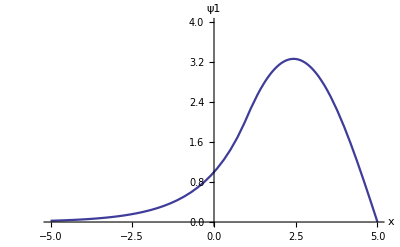

```mathematica
a=5;b=1;ξ=3.0605;η=3.68413;
ϕ1= ⅇ^(η x/a);
ϕ2=(b1 Cos[ξ x/a]+b2 Sin[ξ x/a])/.
{b1->0.264854,b2->3.2589};
ψ1[x_]:=Which[x<b,ϕ1,b≤x≤a,ϕ2];
Plot[ψ1[x],{x,-a,a},PlotRange->{0,4},
AxesLabel->{"x","ψ1"},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[a,b,ξ,η,ψ1,ϕ1,ϕ2]
```

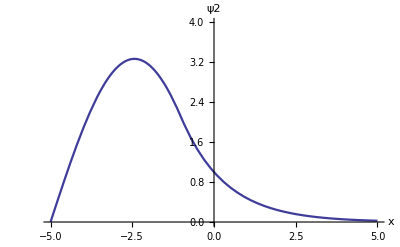

```mathematica
a=5;b=1;ξ=3.0605;η=3.68413;
ϕ1[x_]:= ⅇ^(η x/a);
ϕ2[x_]:=
((b1 Cos[ξ x/a]+b2 Sin[ξ x/a])/.
{b1->0.264854,b2->3.2589});
ψ1[x_]:=Which[x<b,ϕ1[x],b≤x≤a,ϕ2[x]];
ψ2[x_]:=ψ1[-x];
Plot[ψ2[x],{x,-a,a},PlotRange->{0,4},
AxesLabel->{"x","ψ2"},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[a,b,ξ,η,ψ1,ψ2,ϕ1,ϕ2]
```

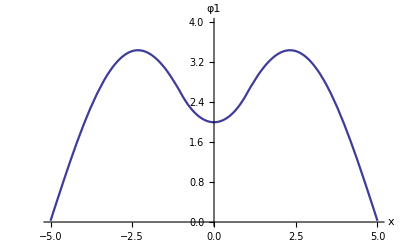

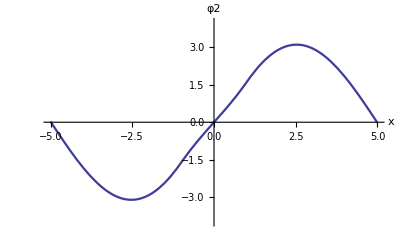

```mathematica
a=5;b=1;ξ=3.0605;η=3.68413;
ϕ1[x_]:= ⅇ^(η x/a);
ϕ2[x_]:=
((b1 Cos[ξ x/a]+b2 Sin[ξ x/a])/.
{b1->0.264854,b2->3.2589});
ψ1[x_]:=Which[x<b,ϕ1[x],b≤x≤a,ϕ2[x]];
ψ2[x_]:=ψ1[-x];
Plot[ψ1[x]+ψ2[x],{x,-a,a},PlotRange->{0,4},
AxesLabel->{"x","φ1"},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[ψ1[x]-ψ2[x],{x,-a,a},PlotRange->{-4,4},
AxesLabel->{"x","φ2"},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[a,b,ξ,η,ψ1,ψ2,ϕ1,ϕ2]
```

```mathematica
a=5*10^-10;b=1*10^-10;m=9.11*10^-31;
V0=3.5*1.6*10^-19;h=1.0545*10^-34;
ξ=3.0605;η=3.68413;
ϕ1[x_]:= ⅇ^(η x/a);
ϕ2[x_]:=
((b1 Cos[ξ x/a]+b2 Sin[ξ x/a])/.
{b1->0.264854,b2->3.2589});
ψ1[x_]:=Which[x<b,ϕ1[x],b≤x≤a,ϕ2[x]];
ψ2[x_]:=ψ1[-x];
V[x_]:=Which[Abs[x]<b,V0,b<=Abs[x]≤a,0];
φ1[x_]:=ψ1[x]+ψ2[x];φ2[x_]:=ψ1[x]-ψ2[x];
Hφ1[x_]:=-h^2/(2 m) D[φ1[x],{x,2}]+V[x] φ1[x];
Hφ2[x_]:=-h^2/(2 m) D[φ2[x],{x,2}]+V[x] φ2[x];
E1=(NIntegrate[φ1[x] Hφ1[x],{x,-a,a}])/
(NIntegrate[φ1[x]^2,{x,-a,a}])/(1.6*10^-19);
E2=(NIntegrate[φ2[x] Hφ2[x],{x,-a,a}])/
(NIntegrate[φ2[x]^2,{x,-a,a}])/(1.6*10^-19);
Print["E(φ1)= ",E1," eV",",",
"  ","E(φ2)= ",E2," eV"]
Clear[a,b,ξ,η,ψ1,ψ2,ϕ1,ϕ2,Hφ1,Hφ2]
```

E(φ1)= 1.24196 eV,  E(φ2)= 1.65518 eV

```mathematica
(*boundary conditions for even symmetry state*)
ϕ1=a1 (ⅇ^(-β x)+ⅇ^(β x));
ϕ2=b1 Cos[ω x]+b2 Sin[ω x];
(ϕ2/.x->a)==0
(D[Log[ϕ1],x]/.x->b)==D[Log[ϕ2],x]/.x->b
Clear[ϕ1,ϕ2]
```

b1 Cos[a ω]+b2 Sin[a ω]==0

(-ⅇ^(-b β) β+ⅇ^(b β) β)/(ⅇ^(-b β)+ⅇ^(b β))==(b2 ω Cos[b ω]-b1 ω Sin[b ω])/(b1 Cos[b ω]+b2 Sin[b ω])

```mathematica
k=b1/b2=-Tan[ω x]=-Tan[ξ]
```

Set::write: Tag Times in -Tan[x\ ω] is Protected.

Set::write: Tag Times in b1/b2 is Protected.

-Tan[ξ]

```mathematica
(-ⅇ^(-b η/a) η+ⅇ^(b η/a) η)/(ⅇ^(-b η/a)+ⅇ^(b η/a))==(ξ Cos[b ξ/a]-k ξ Sin[b ξ])/(k Cos[b ξ/a]+ Sin[b ξ/a])/.
k->-Tan[ξ]
```

(-ⅇ^(-(b η)/a) η+ⅇ^((b η)/a) η)/(ⅇ^(-(b η)/a)+ⅇ^((b η)/a))==(ξ Cos[(b ξ)/a]+ξ Sin[b ξ] Tan[ξ])/(Sin[(b ξ)/a]-Cos[(b ξ)/a] Tan[ξ])

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

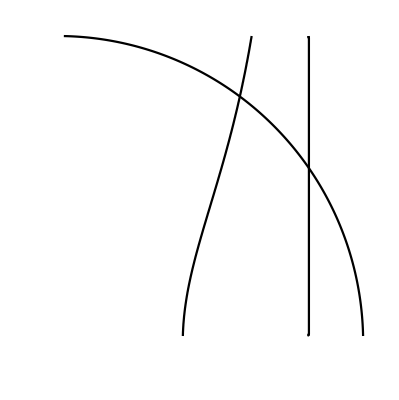

{ξ→2.8578,η→3.84349}

E(even)= 1.24609 eV

```mathematica
a=5*10^-10;b=1*10^-10;m=9.11*10^-31;
V0=3.5*1.6*10^-19;h=1.0545*10^-34;
r=2 m V0 a^2/h^2;equ1=ξ^2+η^2==r;
equ2=
((-ⅇ^(-b η/a) η+ⅇ^(b η/a) η)/(ⅇ^(-b η/a)+ⅇ^(b η/a))==(ξ Cos[b ξ/a]-k ξ Sin[b ξ/a])/(k Cos[b ξ/a]+ Sin[b ξ/a])/.
k->-Tan[ξ]);
<<Graphics`ImplicitPlot`
ImplicitPlot[{equ1,equ2},{ξ,0.1,√r},
{η,0.1,√r},AxesLabel->{"ξ","η"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0}]
s=FindRoot[{equ1,equ2},{ξ,2.5},{η,4}]
Print["E(even)= ",((ξ^2 h^2)/(2 m a^2)/.s)/(1.6*10^-19)," eV"]
Clear[a,b,m,V0,h,r,equ1,equ2]
```

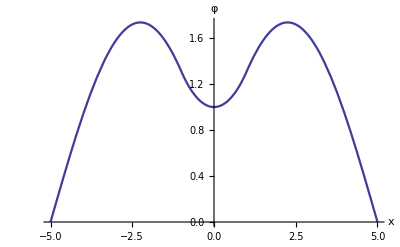

```mathematica
a=5;b=1;V0=3.5;m=9.11 10^-31;h=1.0545 10^-34;
xishu=(2 m 1.6 10^-19 10^-20)/h^2;ξ=1.24609;
V[x_]:=Which[Abs[x]≤b,V0,b<Abs[x]≤a,0];
equ={φ''[x]-xishu (V[x]-ξ) φ[x]==0,φ[0]==1,
φ'[0]==0};s=NDSolve[equ,φ,{x,-a,a}];
Plot[φ[x]/.s[[1]],{x,-a,a},AxesLabel->{"x","φ"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[V0,V,φ,a,b,h,xishu,ξ]
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

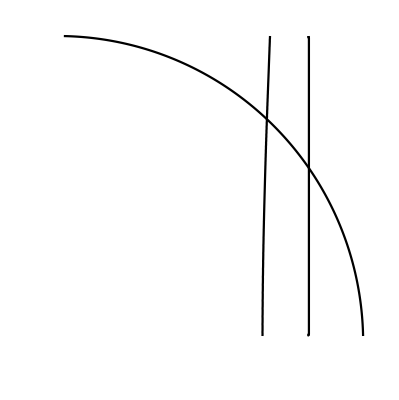

{ξ→3.28202,η→3.48824}

E(odd) = 1.64349 eV

```mathematica
a=5*10^-10;b=1*10^-10;m=9.11*10^-31;
V0=3.5*1.6*10^-19;h=1.0545*10^-34;
r=2 m V0 a^2/h^2;
equ1=ξ^2+η^2==r;
equ2=
((-ⅇ^(-b η/a) η-ⅇ^(b η/a) η)/(ⅇ^(-b η/a)-ⅇ^(b η/a))==(ξ Cos[b ξ/a]-k ξ Sin[b ξ/a])/(k Cos[b ξ/a]+ Sin[b ξ/a])/.
k->-Tan[ξ]);
<<Graphics`ImplicitPlot`
ImplicitPlot[{equ1,equ2},{ξ,0.1,√r},
{η,0.1,√r},AxesLabel->{"ξ","η"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0}]
s=FindRoot[{equ1,equ2},{ξ,3.2},{η,3.5}]
Print["E(odd) = ",((ξ^2 h^2)/(2 m a^2)/.s)/(1.6*10^-19)," eV"]
Clear[a,b,m,V0,h,r,equ1,equ2]
```

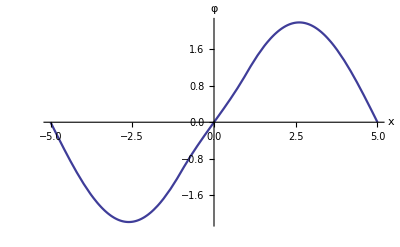

```mathematica
a=5;b=1;V0=3.5;m=9.11 10^-31;h=1.0545 10^-34;
xishu=(2 m 1.6 10^-19 10^-20)/h^2;ξ=1.64349;
V[x_]:=Which[b<Abs[x]≤a,0,Abs[x]≤b,V0];
equ={φ''[x]-xishu (V[x]-ξ) φ[x]==0,φ[0]==0,
φ'[0]==1};
s=NDSolve[equ,φ,{x,-a,a}];
Plot[φ[x]/.s[[1]],{x,-a,a},AxesLabel->{"x","φ"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[V0,V,φ,a,b,h,xishu,ξ]
```

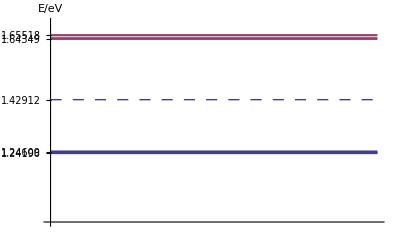

```mathematica
energy1={1.42912};(*single state*)
energy2={1.24196,1.65518};(*perturbation*)
energy3={1.24609,1.64349};(*strict solution*)
energy=Union[energy1,energy2,energy3];
g1=Plot[Evaluate[energy1],{x,0,1},
PlotStyle->{Dashing[{0.02,0.02}]}];
g2=Plot[Evaluate[energy2],{x,0,1},
PlotStyle->{Thickness[0.004]}];
g3=Plot[Evaluate[energy3],{x,0,1},
PlotStyle->{Thickness[0.005]}];
Show[{g1,g2,g3},PlotRange->{1.0,1.7},
Ticks->{None,energy},AxesLabel->{"","E/eV"},
AxesOrigin->{0,1.0},AxesStyle->Thickness[0.003]]
Clear[energy1,energy2,energy3,g1,g2,g3]
```